```mathematica
u=(0.015625-0.03125 ⅇ^(ⅈ ξ)+0.765625 ⅇ^(2 ⅈ ξ)-1.75 ⅇ^(3 ⅈ ξ)+ⅇ^(4 ⅈ ξ))/(d+(0.45572916666666663-3 d) ⅇ^(ⅈ ξ)+(-1.8020833333333333+3 d) ⅇ^(2 ⅈ ξ)+(1.5963541666666665-d) ⅇ^(3 ⅈ ξ));
```

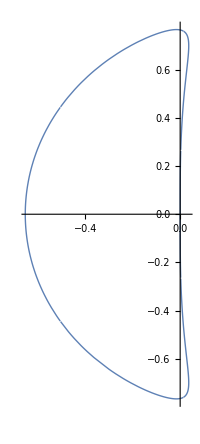

```mathematica
d=-0.2;
p1=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->Thick
,AxesOrigin->{0,0}
,PlotRange->All]
```

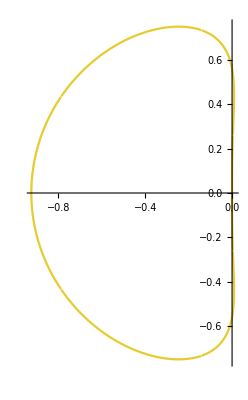

```mathematica
d=0;
p2=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->RGBColor[0.9,0.8,0.19]
,AxesOrigin->{0,0}
,PlotRange->All]
```

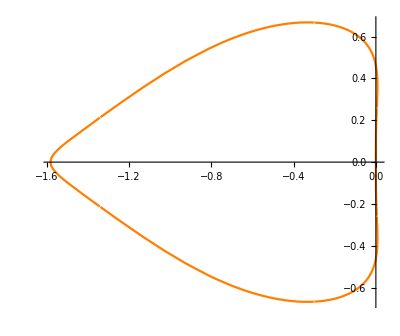

```mathematica
d=0.2;
p3=ParametricPlot[{Re[u],Im[u]}
,{ξ,0,2π}
,PlotStyle->Orange
,AxesOrigin->{0,0}
,PlotRange->All]
```

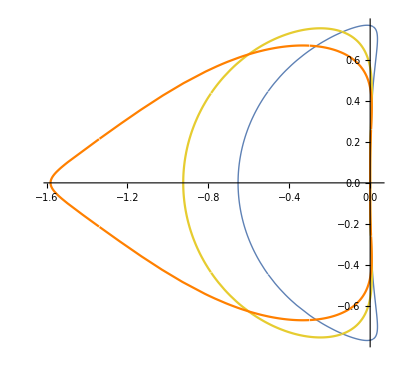

```mathematica
Show[p1,p2,p3]
```

```mathematica
Show[%29,ImageSize->Large,AxesLabel->{Style[Re,Medium],Style[Im,Medium]},AxesStyle->{{Arrowheads[0.03],AbsoluteThickness[1]}, {Arrowheads[0.03],AbsoluteThickness[1]}}]
```